```mathematica
encodeID[expr_]:=StringReplace[Developer`EncodeBase64@BinarySerialize@expr,"/"->"~"]
decodeID[expr_]:=BinaryDeserialize@Developer`DecodeBase64ToByteArray@StringReplace[expr,"~"->"/"]
```

```mathematica
ClearAll[getFileNames,fromFileNameGetGeoRange]

getFileNames[folderName_] := 
	FileNames["*.png",FileNameJoin[{NotebookDirectory[],folderName}],Infinity];

fromFileNameGetGeoRange[fileName_] := 
	decodeID[FileBaseName@fileName]["GeoRange"];
```

```mathematica
ClearAll[associateFilesToGeoRange]
associateFilesToGeoRange[fileNames_] := 
	Map[
		File[#] -> fromFileNameGetGeoRange[#] &,
		getFileNames[fileNames]
	]
```

```mathematica
calculateError[net_,data_] :=(Abs[net[data[[All,1]]]-data[[All,2]]])/data[[All,2]]//Mean
calculateMeanSq[net_,data_] :=(Abs[net[data[[All,1]]]-data[[All,2]]])^2//Mean
```

```mathematica
ClearAll[sortPerformance]
sortPerformance[net_,data_] := 
	With[
		{img = Map[Import,data[[All,1]]], correspondingScale = data[[All,2]]},
		SortBy[
			AssociationThread[img,Transpose[{net[img],correspondingScale}]],
			Abs[First[#] - Last[#]]&
		]
	]
```

Training | Validation | Testing
11494 | 1050 | 420

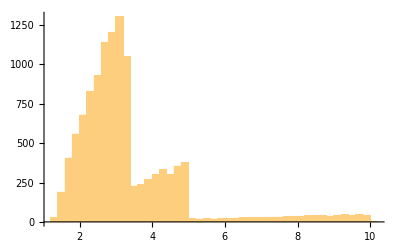
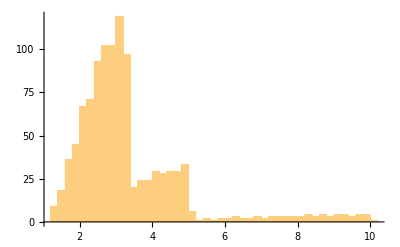
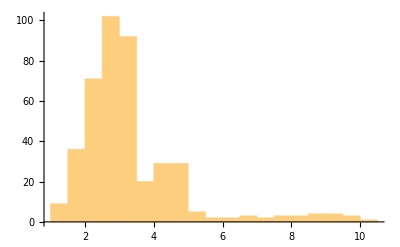
Training Data distribution | Validation Data distribution | Testing Data distribution
-Graphics- | -Graphics- | -Graphics-

```mathematica
ClearAll[training3,validation3,testing3]

training3 = RandomSample@associateFilesToGeoRange["training"];
validation3 = RandomSample@associateFilesToGeoRange["validation"];
testing3 = RandomSample@associateFilesToGeoRange["testing"];

TableForm[
	{{"Training","Validation","Testing"},
	{Length@training3,Length@validation3,Length@testing3}}
]

TableForm[
	{{"Training Data distribution","Validation Data distribution","Testing Data distribution"},
	{Histogram[Sort@training3[[All,2]],PlotRange->All],Histogram[Sort@validation3[[All,2]],PlotRange->All],Histogram[Sort@testing3[[All,2]],PlotRange->All]}}
]
```

```mathematica
ClearAll[tnet3]
tnet3 = Import["/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/wolframScriptCodes/moreImagesToTrain2/progress/2018-07-10T07:28:10_0_25_11975_3.47e-2_1.12e-1.wlnet"]
(*tnet = Import["/Users/mehmetsahin/Desktop/wolframscpt/more/moreImagesToTrain/progress/2018-07-09T20:54:19_0_30_12270_1.04e-2_4.34e-2.wlnet"]*)
```

NetChain[<>]

```mathematica
ClearAll[dataset3]
dataset3 = sortPerformance[tnet3,testing3];
dataset3[[1;;3]]  (*Best 3*)
dataset3[[-3;;]] (*Worst 3*)
```

<|-Graphics-→{3.16445,3.16293},-Graphics-→{1.84887,1.84603},-Graphics-→{1.94567,1.94263}|>

<|-Graphics-→{6.91223,4.17747},-Graphics-→{7.29591,4.17747},-Graphics-→{7.86428,4.61047}|>

```mathematica
Column[{Row[
	{Style["Best->   ",14,Bold],First@dataset3[[1]],
	Column[{Style[Row[
	{"Real Scale:   ",ToString@First@Last@dataset3[[1]]}],13],
	Style[Row[
	{"Predicted :   ",ToString@Last@Last@dataset3[[1]]}],13],Style[Row[
	{"Error     :   ","0.04%"}],13]}],"    ",Column[{First@dataset3[[2]],
	Style[Row[
	{"Real Scale:   ",ToString@First@Last@dataset3[[2]]}],13],
	Style[Row[
	{"Predicted :   ",ToString@Last@Last@dataset3[[2]]}],13],Style[Row[
	{"Error     :   ","0.15%"}],13]}]}
],"   ",Row[
	{Style["Worst->  ",14,Bold],Column[{First@dataset3[[-1]],
	Style[Row[
	{"Real Scale:   ",ToString@First@Last@dataset3[[-1]]}],13],
	Style[Row[
	{"Predicted :   ",ToString@Last@Last@dataset3[[-1]]}],13],Style[Row[
	{"Error     :   ","41.37%"}],13]}],"    ",Column[{First@dataset3[[-2]],
	Style[Row[
	{"Real Scale:   ",ToString@First@Last@dataset3[[-2]]}],13],
	Style[Row[
	{"Predicted :   ",ToString@Last@Last@dataset3[[-2]]}],13],Style[Row[
	{"Error     :   ","42.74%"}],13]}]}
]}]
```

Best->   -Graphics-Real Scale:   3.16445
Predicted :   3.16293
Error     :   0.04%    -Graphics-
Real Scale:   1.84887
Predicted :   1.84603
Error     :   0.15%
   
Worst->  -Graphics-
Real Scale:   7.86428
Predicted :   4.61047
Error     :   41.37%    -Graphics-
Real Scale:   7.29591
Predicted :   4.17747
Error     :   42.74%

```mathematica
Round[100-57.2576964354001,0.01]
```

42.74

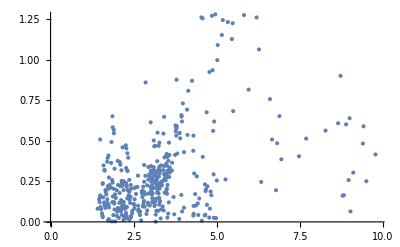

```mathematica
ListPlot[Transpose[{Map[First[#]&,Values[dataset1]],Map[Abs[First[#]-Last[#]]&,Values[dataset3]]}]]
```

### There should be an issue here....

```mathematica
calculateError[tnet3,testing]
```

0.0806686

```mathematica
calculateError[tnet,testing]
```

0.0806686

All

```mathematica
tr = Join[trainSmall,training2,training3];
vl = Join[validationSmall,validation1,validation2];
te = Join[testSmall,testing1,testing2];

tr // Length
vl // Length
te // Length
```

33162

5125

2460

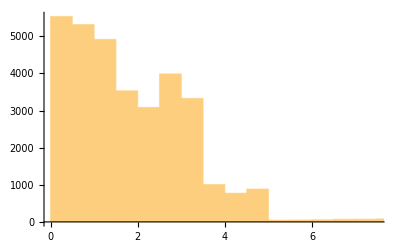
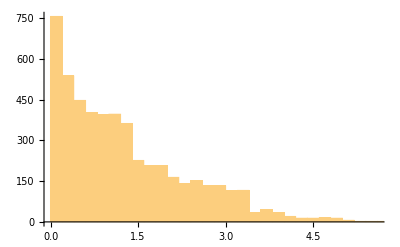
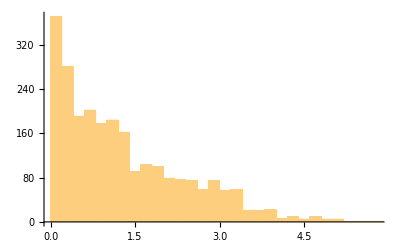
Training Data distribution | Validation Data distribution | Testing Data distribution
-Graphics- | -Graphics- | -Graphics-

```mathematica
TableForm[
	{{"Training Data distribution","Validation Data distribution","Testing Data distribution"},
	{Histogram[tr[[All,2]]],Histogram[vl[[All,2]]],Histogram[te[[All,2]]]}}
]
```

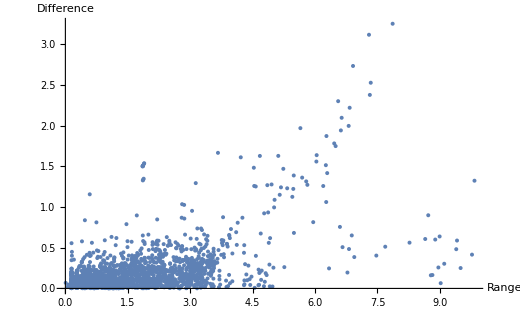

```mathematica
dt = Join[dataset1,dataset2,dataset3];
ListPlot[Transpose[{Map[First[#]&,Values[dt]],Map[Abs[First[#]-Last[#]]&,Values[dt]]}],AxesLabel->{Style["Range",15,Black],Style["Difference",15,Black]},PlotRange->All]
```

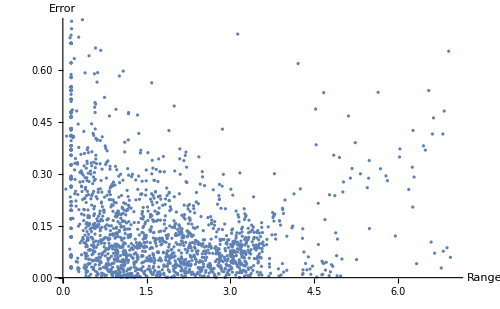

```mathematica
dt = Join[dataset1,dataset2,dataset3];
ListPlot[Transpose[{Map[First[#]&,Values[dt]],Map[Abs[First[#]-Last[#]]/Last[#]&,Values[dt]]}],AxesLabel->{Style["Range",15,Black],Style["Error",15,Black]}]
```

```mathematica
allTest = Join[testSmall,testing2,testing3];
calculateError[tnet3,allTest]
```

2.59479